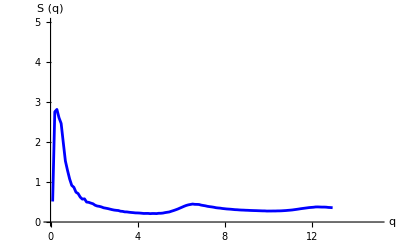

```mathematica
data=Import["/home/claudia/Documents/Investigación/Pruebas/SF_Fran/phi_01/sf0.dat"];
ListPlot[data[[All,{1,2}]],AxesLabel->{"q","S (q)"},PlotStyle->Blue,PlotRange->{{0,15},{0,5}},Joined->True ]
```

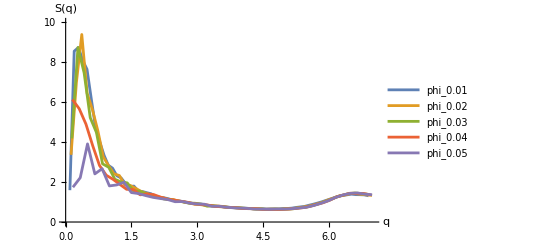

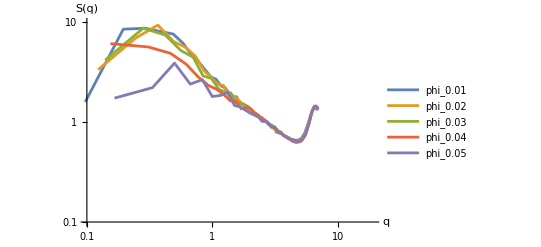

```mathematica
Dir="/home/claudia/Documents/Investigación/Pruebas/SF_Fran/phi_0";

data=Table[Import[Dir<>ToString[i]<>"/sf_slow.dat"][[All,{1,2}]],{i,1,5}];
ListLinePlot[data,AxesLabel->{"q","S(q)"},PlotRange->{{0,7},{0,10}},PlotLegends->Table["phi_0.0"<>ToString[i],{i,1,5}]]
ListLinePlot[data,AxesLabel->{"q","S(q)"},PlotRange->{{0.1,19},{0.1,10}},ScalingFunctions->{"Log","Log"},PlotLegends->Table["phi_0.0"<>ToString[i],{i,1,5}]]
```

```mathematica
data=First[data]
```

{{0.245,5.12655},{0.368,9.58147},{0.49,6.51972},{0.613,5.58748},{0.736,4.55702},{0.858,3.26879},{0.981,2.8219},{1.103,2.40652},{1.226,2.3301},{1.349,1.85351},{1.471,1.83691},{1.594,1.69141},{1.717,1.53858},{1.839,1.43563},{1.962,1.34556},{2.084,1.25394},{2.207,1.22662},{2.33,1.13178},{2.452,1.12719},{2.575,1.05389},{2.697,1.00333},{2.82,0.955667},{2.943,0.88784},{3.065,0.872566},{3.188,0.837763},{3.31,0.821599},{3.433,0.810018},{3.556,0.785722},{3.678,0.732612},{3.801,0.72289},{3.924,0.714944},{4.046,0.691174},{4.169,0.682506},{4.291,0.658827},{4.414,0.658599},{4.537,0.635282},{4.659,0.646225},{4.782,0.6495},{4.904,0.640894},{5.027,0.665228},{5.15,0.672311},{5.272,0.703664},{5.395,0.738974},{5.517,0.78551},{5.64,0.846736},{5.763,0.922823},{5.885,1.0117},{6.008,1.12492},{6.13,1.21307},{6.253,1.31946},{6.376,1.35734},{6.498,1.42508},{6.621,1.42029},{6.744,1.38787},{6.866,1.35962},{6.989,1.334},{7.111,1.29243},{7.234,1.24268},{7.357,1.19434},{7.479,1.15226},{7.602,1.12433},{7.724,1.08748},{7.847,1.04865},{7.97,1.03881},{8.092,1.02238},{8.215,0.999135},{8.337,0.984977},{8.46,0.969306},{8.583,0.960434},{8.705,0.938366},{8.828,0.921481},{8.951,0.912943},{9.073,0.899276},{9.196,0.886943},{9.318,0.881447},{9.441,0.865837},{9.564,0.877149},{9.686,0.862822},{9.809,0.851146},{9.931,0.855126},{10.054,0.844492},{10.177,0.845264},{10.299,0.846173},{10.422,0.853552},{10.544,0.86896},{10.667,0.870588},{10.79,0.878477},{10.912,0.894021},{11.035,0.914058},{11.158,0.934724},{11.28,0.961815},{11.403,0.993327},{11.525,1.03613},{11.648,1.07566},{11.771,1.10441},{11.893,1.124},{12.016,1.15141},{12.138,1.17255},{12.261,1.17055},{12.384,1.17861},{12.506,1.17738},{12.629,1.1637},{12.751,1.15637},{12.874,1.1347},{12.997,1.11915}}

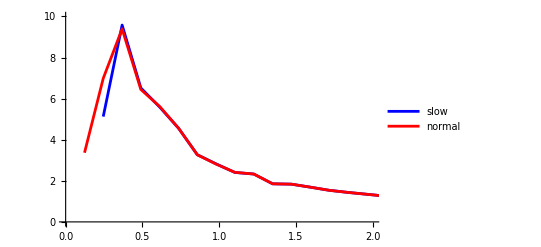

```mathematica
datanew=Import["/home/claudia/Documents/Investigación/Pruebas/SF_Fran/phi_02/sf_slow.dat"][[All,{1,2}]];
ListLinePlot[{data,datanew},PlotStyle->{Blue,Red},PlotLegends->{"slow","normal"},PlotRange->{{0,2},{0,10}}]
```

```mathematica
data=First[data];
Dimensions[datanew]
Dimensions[data]
```

{57,2}

{105,2}